# Quantum Potato Chips

```mathematica
Quit
```

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

```mathematica
Get["Wolfram`QuantumFramework`"]
```

## 1. Introduction

### Figures

Simplex projection to its lower dimension by rotation.

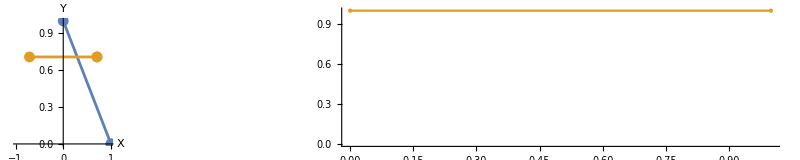

```mathematica
GraphicsRow[
{
ListLinePlot[
{{{0,1},{1,0}},RotationTransform[{{1,1},{0,1}}]@{{0,1},{1,0}}},
Mesh->All,Ticks->None,PlotRange->{{-1,1},{0,1}},AspectRatio->1/2,AxesLabel->{"X","Y"}
],

Framed["\!\(\*OverscriptBox[\(⟶\), SubscriptBox[\(U\), \(rot\)]]\)",FrameStyle->None],NumberLinePlot[Interval[{0,1}],PlotStyle->ColorData[97][2]]
}]
```

```mathematica
GraphicsRow[{

Graphics3D[
{#,TranslationTransform[{0,0,-1/Sqrt[3]}]@RotationTransform[{ConstantArray[1,3],UnitVector[3,3]}]@#}
&@Simplex[IdentityMatrix[3]],
Axes->True,AxesLabel->{"X","Y","Z"},
Ticks->None,ViewPoint->{3,-1,1}
],

Framed["\!\(\*OverscriptBox[\(⟶\), SubscriptBox[\(U\), \(rot\)]]\)",FrameStyle->None],TernaryListPlot[{},Method->{"Backdrop"->LightOrange}]
}]
```

-Graphics-

```mathematica
GraphicsRow[{
Style[MatrixForm@IdentityMatrix[4],30],

Framed["→^U_rot",FrameStyle->None],

Graphics3D[
{
Opacity[.5],Simplex@RotationTransform[{ConstantArray[1,4],UnitVector[4,1]}][IdentityMatrix[4]][[All,2;;]]
},
Boxed->False,

Epilog->{
AxisObject[Line[{{.03,0.15},{0.23,.83}}],{0,1},TickDirection->"Inward",TickLengths->0],AxisObject[Line[{{.77,0.15},{.03,0.15}}],{0,1},TickDirection->"Inward",TickLengths->0],AxisObject[Line[{{.03,0.15},{.6,0.67}}],{0,1},TickLabels->None,TickLengths->0]
}]
}]
```

-Graphics-

## 2. Generating Quantum Potato Chips

## 2.1 SIC-POVM Case

### Equations

Consider a rotation matrix which represents a 4D rotation by 𝜃 in the plane spanned by {1, 1, 1, 1} and {1, 0, 0, 0}:

Equation 1 :

```mathematica
rot=RotationMatrix[θ,{{1,1,1,1},{1,0,0,0}}];
rot//MatrixForm
```

(Cos[θ] | Sin[θ]/(√3) | Sin[θ]/(√3) | Sin[θ]/(√3)
-Sin[θ]/(√3) | 1/3 (2+Cos[θ]) | 1/3 (-1+Cos[θ]) | 1/3 (-1+Cos[θ])
-Sin[θ]/(√3) | 1/3 (-1+Cos[θ]) | 1/3 (2+Cos[θ]) | 1/3 (-1+Cos[θ])
-Sin[θ]/(√3) | 1/3 (-1+Cos[θ]) | 1/3 (-1+Cos[θ]) | 1/3 (2+Cos[θ]))

For the special case of θ=π/3:

Equation 2:

```mathematica
rotation=rot/.θ->π/3;
rotation//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
-1/2 | 5/6 | -1/6 | -1/6
-1/2 | -1/6 | 5/6 | -1/6
-1/2 | -1/6 | -1/6 | 5/6)

Probability vector transformation:

```mathematica
rotation.{p1,p2,p3,1-(p1+p2+p3)}//Simplify
```

{1/2,-1/6-p1/3+p2,-1/6-p1/3+p3,1/6 (5-8 p1-6 p2-6 p3)}

Original 3-simplex transformation:

```mathematica
rotation.Permutations[{1,0,0,0},{4}]
```

{{1/2,1/2,1/2,1/2},{-1/2,5/6,-1/6,-1/6},{-1/2,-1/6,5/6,-1/6},{-1/2,-1/6,-1/6,5/6}}

The transformed simplex can be projected into ℝ^3 space, as a tetrahedron spanned by:

```mathematica
Rest/@%
```

{{1/2,1/2,1/2},{5/6,-1/6,-1/6},{-1/6,5/6,-1/6},{-1/6,-1/6,5/6}}

Consider two points randomly sampled from a 1-simplex spanned by points {1,0} and {0,1}:

Equation 3:

```mathematica
product=KroneckerProduct[{p,1-p},{q,1-q}]//Flatten
```

{p q,p (1-q),(1-p) q,(1-p) (1-q)}

Transform eq.(3) using eq.(2):

Equation 4:

```mathematica
surface4d=rotation.product//ComplexExpand
```

{1/2,-1/6+p-(4 p q)/3,-1/6+q-(4 p q)/3,5/6-p-q+(2 p q)/3}

Drop the first element to obtain the three-dimensional surface from a tetrahedron of probability space:

Equation 5:

```mathematica
surface=Rest[surface4d]
```

{-1/6+p-(4 p q)/3,-1/6+q-(4 p q)/3,5/6-p-q+(2 p q)/3}

The only region of this tetrahedron that corresponds to physical quantum states is the sphere that is inscribed within it. The intersection of the insphere and the surface in eq.(5), is what we called as quantum potato chip:

Equation 6:

```mathematica
boundary=Normal[Solve[Norm[2 √3 surface]==1,q,Reals]]
```

{{q→1/2-(√((-1+6 p-6 p^2)/(1-2 p+2 p^2)))/(2 √3)},{q→1/2+(√((-1+6 p-6 p^2)/(1-2 p+2 p^2)))/(2 √3)}}

The quantum potato chip is a surface described in eq.(5) and parameterized by 𝑝, 𝑞 as follow:

Equation 7:

```mathematica
{0<=p<=1,First[#]<=q<=Last[#]&@Values[Flatten@boundary]}
```

{0≤p≤1,1/2-(√((-1+6 p-6 p^2)/(1-2 p+2 p^2)))/(2 √3)≤q≤1/2+(√((-1+6 p-6 p^2)/(1-2 p+2 p^2)))/(2 √3)}

In 3 dimensions, the 3 possible 1-simplex are given by {{1,0,0},{0,1,0}} (as in eq. 3), {{1,0,0},{0,0,1}}, and {{0,1,0},{0,0,1}}.

Equation 8 & 9:

```mathematica
products=Permute[product,#]&/@{{1,4,2,3},{3,1,2,4}};
surfaces=ComplexExpand[Rest[rotation.#]&/@products]
```

{{-1/6+q-(4 p q)/3,5/6-p-q+(2 p q)/3,-1/6+p-(4 p q)/3},{-1/6-p/3+q-(2 p q)/3,-1/6-p/3+(4 p q)/3,5/6-(4 p)/3-q+(4 p q)/3}}

### Figures

#### Figure 2a

A 1-simplex as the lowest dimensional probability space

1-simplex defined by the points {1, 0}, {0, 1} (solid blue line):

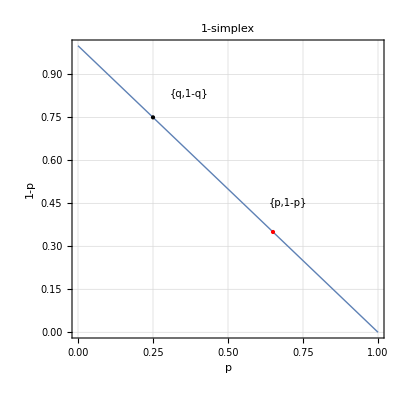

```mathematica
Graphics[{
{Text[Style["{q,1-q}",10],{.37,.83}],Text[Style["{p,1-p}",10],{.7,.45}]},
{ColorData[97][1],Simplex[{{1,0},{0,1}}]},{Black,Point[{.25,.75}]},
{Red,Point[{.65,.35}]}
},
	Axes->True,AxesOrigin->{0,0},
	AxesLabel->{"p","1-p"},PlotLabel->"1-simplex",
	Frame->True,GridLines->Automatic,FrameTicks->{{Automatic,None},{Automatic,None}}
]
```

#### Figure 2b

Intersection of tetrahedron and surface of two 1-simplex probability spaces

The blue solid line represents 1-simplex (same as in Figure 2a). The surface, described by eq.(5), lies entirely within the 2-simplex (a tetrahedron).The solid red line represents the intersection of this surface with the tetrahedron’s insphere. Only the points within the insphere correspond to valid physical quantum states.

```mathematica
Show[
	Graphics3D[
	{
	{Opacity[.5],Ball[{0,0,0},1/(2 Sqrt[3])]},
	{ColorData[97][1],Thickness[.005],Simplex[{{1,0,0},{0,1,0}}]}
	},
	Axes->True,AxesOrigin->{0,0,0},Boxed->False
	],

	ParametricPlot3D[surface/. boundary,{p,0,1},Mesh->None,PlotStyle->Red],
	ParametricPlot3D[surface,{p,0,1},{q,0,1},PlotStyle->{Opacity[0.6]}],

ImageSize->400]
```

-Graphics3D-

#### Figure 2c

Three quantum potato chips

Quantum potato chips are defined in eq.(5), eq.(8), and eq.(9), and parametrized by eq.(7). With one such surface in hand, one can find the other two through proper permutation of variables.

```mathematica
ParametricPlot3D[
Evaluate[Prepend[surfaces,surface]],
{p,0,1},
Prepend[Flatten[Values[boundary]],q],
Mesh->None,PlotStyle->Opacity[.5],PlotPoints->200,Boxed->False,Axes->False,ImageSize->200]
```

-Graphics3D-

## 2.2 Bloch Sphere

### Equations

Consider the following SIC-POVM:

Equation 10:

```mathematica
SICPOVM=(Normal[Chop[#]]&/@Reverse[QuantumMeasurementOperator["QBismSICPOVM"]["Conjugate"]["POVMElements"]])/.x_?NumericQ:>(#1+#2I&@@RootApproximant[ReIm[x]]);
QBismSICPOVM=AssociationThread[{Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4]}->(SICPOVM)];
MatrixForm/@QBismSICPOVM
```

<|𝒬_1→(1/12 (3-√3) | -(1/4+ⅈ/4)/(√3)
-(1/4-ⅈ/4)/(√3) | 1/12 (3+√3)),𝒬_2→(1/12 (3-√3) | (1/4+ⅈ/4)/(√3)
(1/4-ⅈ/4)/(√3) | 1/12 (3+√3)),𝒬_3→(1/12 (3+√3) | -(1/4-ⅈ/4)/(√3)
-(1/4+ⅈ/4)/(√3) | 1/12 (3-√3)),𝒬_4→(1/12 (3+√3) | (1/4-ⅈ/4)/(√3)
(1/4+ⅈ/4)/(√3) | 1/12 (3-√3))|>

The corresponding phase-space basis matrix for this SIC-POVM is given by

Equation 11:

```mathematica
ℬ=Reverse[QuantumBasis["QBismSIC"]["Conjugate"]["Elements"]]/.x_?NumericQ:>(#1+#2I&@@RootApproximant[ReIm[x]]);
MatrixForm/@Flatten/@ℬ
```

{(1/2 (1-√3)
(-1/2-ⅈ/2) √3
(-1/2+ⅈ/2) √3
1/2 (1+√3)),(1/2 (1-√3)
(1/2+ⅈ/2) √3
(1/2-ⅈ/2) √3
1/2 (1+√3)),(1/2 (1+√3)
(-1/2+ⅈ/2) √3
(-1/2-ⅈ/2) √3
1/2 (1-√3)),(1/2 (1+√3)
(1/2-ⅈ/2) √3
(1/2+ⅈ/2) √3
1/2 (1-√3))}

Given a probability vector p⃗={p_1,p_2,p_3,1-(p_1+p_2+p_3)} in the basis of eq.(11), the vectorized density matrix is given by:

Equation 12:

```mathematica
pvector={p1,p2,p3,1-(p1+p2+p3)};
ρ=Transpose[Flatten/@ℬ].pvector//FullSimplify//Chop;
ρ//MatrixForm
```

(1/2 (1+√3-2 √3 p1-2 √3 p2)
(1/2+ⅈ/2) √3 (-ⅈ-(1-ⅈ) p1+(1+ⅈ) p2+2 ⅈ p3)
(1/2+ⅈ/2) √3 (1-(1-ⅈ) p1-(1+ⅈ) p2-2 p3)
1/2-(√3)/2+√3 p1+√3 p2)

Density matrix eigenvalues are:

Equation 13:

```mathematica
ρmatrix=ArrayReshape[ρ,{2,2}];
FullSimplify[Eigenvalues[ρmatrix]]//TableForm
```

1/2 (1-√3 √(3-8 p2-8 p3+8 (p1^2+p2^2+p2 p3+p3^2+p1 (-1+p2+p3))))
1/2 (1+√3 √(3-8 p2-8 p3+8 (p1^2+p2^2+p2 p3+p3^2+p1 (-1+p2+p3))))

Compare the vectorized density matrix in the Bloch sphere with its counterpart in the phase-space as expressed in eq.(12) and find the relation between vector p⃗ and the Bloch vector {x,y,z}:

Equation 14:

```mathematica
xyzvector=QuantumState["BlochVector"[{x,y,z}]];
Solve[xyzvector["StateVector"]==ρ,{p1,p2,p3}]
```

{{p1→1/12 (3-√3 x+√3 y-√3 z),p2→1/12 (3+√3 x-√3 y-√3 z),p3→1/12 (3-√3 x-√3 y+√3 z)}}

Equation 15:

```mathematica
Solve[xyzvector["StateVector"]==ρ,{x,y,z}]
```

{{x→√3-2 √3 p1-2 √3 p3,y→√3-2 √3 p2-2 √3 p3,z→√3-2 √3 p1-2 √3 p2}}

Parametrize the boundary of the quantum potato chip in the Bloch sphere using the  Weyl–Wigner transformation:

Equation 16:

```mathematica
state=QuantumWeylTransform[QuantumState[product,ℬ,"Parameters"->{p,q}]];
r=FullSimplify[state["BlochVector"]/.#&/@boundary]
```

{{√(-3+2/(1+2 (-1+p) p)),(1-2 p) √(-3+2/(1+2 (-1+p) p)),√3 (1-2 p)},{-√(-3+2/(1+2 (-1+p) p)),(-1+2 p) √(-3+2/(1+2 (-1+p) p)),√3 (1-2 p)}}

### Figures

#### Extra Definitions

```mathematica
(*This could be added into the framework?*)
blochsphere=Show[
Graphics3D[{

{Opacity[0.2],Sphere[]},
	
Black,Thickness[0.001],Opacity[1.0],

Splice@{Line[{{0,1,0},{0,-1,0}}],Line[{{0,0,1},{0,0,-1}}],Line[{{1,0,0},{-1,0,0}}]},

Splice@{Text[Ket[{0}],{0,0,1.05}],Text[Ket[{1}],{0,0,-1.05}],Text[Ket[{"R"}],{0,1.05,0}],Text[Ket[{"L"}],{0,-1.05,0}],Text[Ket[{"+"}],{1.05,0,0}],Text[Ket[{"-"}],{-1.05,0,0}]} 

},Boxed->False],

ParametricPlot3D[{{Cos[t],Sin[t],0},{0,Cos[t],Sin[t]},{Cos[t],0,Sin[t]}},{t,0,2 Pi},PlotStyle->ConstantArray[{Black,Thin},3]]

];
```

```mathematica
QBism=Map[QuantumState[#]["BlochVector"]&,SICPOVM];
```

```mathematica
ℬpoints=Map[QuantumState[#]["BlochVector"]&,ℬ];
```

#### Image 3a

QBism SIC-POVM basis element and its POVM elements in Bloch sphere

SIC-POVM basis (ℬ_i, blue) vs POVM elements (𝒬_i, green), represented in the Bloch sphere. Note the ℬ_i tetrahedron represents the available phase-space, spanned by QBism SIC-POVM basis, while the POVM elements are within the insphere.

```mathematica
Show[
blochsphere,
Graphics3D[{
{MapIndexed[{PointSize[0.01],Sphere[#1,.05],Black,Text[Subscript["ℬ",#2[[1]]],1.05 #1]}&,ℬpoints],
{Opacity[.2],FaceForm[None],EdgeForm[{Opacity[.5],Thick,ColorData[97][1]}],Tetrahedron[ℬpoints]}},

{ColorData[97][3],
MapIndexed[{PointSize[0.01],Sphere[#1,.05],Black,Text[Subscript["𝒬",#2[[1]]],1.2 #1]}&,QBism],{Opacity[.5],EdgeForm[{Thick,ColorData[97][3]}],Tetrahedron[QBism]}}
},Boxed->False]
]
```

-Graphics3D-

#### Image 3b

Quantum potato chip and QBism SICPOVM elements in Bloch sphere.

The green spheres are Bloch vectors for the QBism SIC-POVM in eq.(11).

```mathematica
Show[
Graphics3D[
{
ColorData[97][3],MapIndexed[{PointSize[0.01],Sphere[#1,.05],Black,Text[Subscript["𝒬",#2[[1]]],1.2 #1]}&,2*QBism],{Opacity[.5],EdgeForm[{Thick,ColorData[97][3]}],Tetrahedron[2*QBism]}
},
Boxed->False
],

ParametricPlot3D[Evaluate[state["BlochVector"]]/. boundary,{p,0,1},PlotStyle->Red],

ParametricPlot3D[Evaluate[state["BlochVector"]],{p,0,1},{q,Sequence@@boundary[[All,-1,-1]]},PlotPoints->200,Mesh->None,PlotStyle->Opacity[.7]],

blochsphere

]
```

-Graphics3D-

#### Image 3c

Quantum potato chips and three new POVM elements

The solid red line is the boundary of quantum potato chip, while sphere represents new POVM defined in eq.(20).

```mathematica
Legended[
Show[
blochsphere,

ParametricPlot3D[r,{p,0,1},PlotStyle->Red],

Graphics3D[
{Opacity[.5],Green,Sphere[#,.05]&/@{{1/Sqrt[3],0,0},{-(1/Sqrt[3]),0,0}},
Blue,Sphere[#,.05]&/@{{0,-(1/Sqrt[3]),0},{0,1/Sqrt[3],0}},
Cyan,Sphere[#,.05]&/@{{0,0,1/Sqrt[3]},{0,0,-(1/Sqrt[3])}}
}
]
],

Placed[
SwatchLegend[
{Green,Blue,Cyan},
{Subscript[ℳ, 1],Subscript[ℳ, 2],Subscript[ℳ, 3]}],{.95,.85}
]
]
```

-Graphics-

## 3. Quantum Potato Chip as Self-Correlation-Free States

## 3.1 Matthews correlation of classical binary variables

### Definitions

Definition of Matthews correlation:

```mathematica
Phi[dist_CategoricalDistribution]:=Phi[Information[dist,"ProbabilityArray"]]
```

```mathematica
Phi[p_?MatrixQ]/;Dimensions[p]=={2,2}:=(p⟦2,2⟧ p⟦1,1⟧-p⟦1,2⟧ p⟦2,1⟧)/(√((p⟦1,1⟧+p⟦1,2⟧) (p⟦2,1⟧+p⟦2,2⟧) (p⟦1,1⟧+p⟦2,1⟧) (p⟦1,2⟧+p⟦2,2⟧)))
```

Matthews correlation is zero for two disjoint probability distributions:

```mathematica
Phi[CategoricalDistribution[{{1,2},{1,2}},ArrayReshape[product,{2,2}]]]//Simplify
```

0

### Equations

Given binary variables defining the probability vector as

Equation 17:

```mathematica
pvector->MatrixForm[ArrayReshape[pvector,{2,2}]]
```

{p1,p2,p3,1-p1-p2-p3}→(p1 | p2
p3 | 1-p1-p2-p3)

The corresponding Matthews correlation coefficient is given by

Equation 18:

```mathematica
Phi[CategoricalDistribution[{{1,2},{1,2}},ArrayReshape[pvector,{2,2}]]]
```

(p1 (1-p1-p2-p3)-p2 p3)/(√((1-p1-p2) (p1+p2) (1-p1-p3) (p1+p3)))

```mathematica
phi=FullSimplify@Phi@ArrayReshape[QuantumPhaseSpaceTransform[xyzvector,QuantumBasis[ℬ]]["AmplitudesList"],{2,2}]//Chop
```

(√3 y-x z)/(√((-3+x^2) (-3+z^2)))

The eq.(18) takes a more natural form if Bloch sphere’s radius is 1/(√3):

Equation 19:

```mathematica
FullSimplify@Phi@ArrayReshape[QuantumPhaseSpaceTransform[QuantumState["BlochVector"[√3{x,y,z}]],QuantumBasis[ℬ]]["AmplitudesList"],{2,2}]//Chop
```

(y-x z)/(√((-1+x^2) (-1+z^2)))

### Figures

#### Figure 4

Matthews correlation coefficient eq.(18) for the pair of binary variables forming the probability vector eq.(17). 𝜑 has minimum  -1/(√3) and maximum 1/(√3) at the poles of the sphere

φ = 0 corresponds to the Quantum Potato Chip (green contour):

```mathematica
Show[
	
	Graphics3D[
		{Opacity[.5],Sphere[]}
	],
	
	ContourPlot3D[phi,{x,-1,1},{y,-1,1},{z,-1,1},
		Contours->N@Range[-1/2,1/2,1/4],
		RegionFunction->Function[{x,y,z},x^2+y^2+z^2<1],
		Mesh->None,
		RegionBoundaryStyle->None,
		PlotLegends->SwatchLegend[Automatic,LegendLayout->"ReversedColumn"],
		PlotRangePadding->None
	],

Boxed->False,Axes->False
]
```

-Graphics3D-

```mathematica
Show[
	Graphics3D[{
	{Text[Ket[{"↑"}],{0,0,1.3}],
	Text[Ket[{"↓"}],{0,0,-1.3}],
	Text[Ket[{"→"}],{1.3,0,0}]}}
	],

	SliceContourPlot3D[phi,"CenterSphere",{x,y,z}∈Ball[],
	Contours->5,
	ColorFunction->Function[x,Opacity[1,ColorData["SunsetColors"][x]]],
	ContourStyle->Directive[Thick,Black],
	PlotLegends->Automatic,
	PlotPoints->10,
	RegionFunction->Function[{x,y,z,f},x<0]
	],

Boxed->False]
```

-Graphics3D-

## 3.2 Construction of Quantum State by Projective Measurements

### Equations

Obtain Bloch Vectors for linear combinations of POVM showing Cartesian directions:

Equation 20:

```mathematica
ops=With[
{op=QBismSICPOVM[#1]+QBismSICPOVM[#2]},
Simplify[{Normal[op],IdentityMatrix[2]-op}]
]&@@@{{Subscript[𝒬, 1],Subscript[𝒬, 2]},{Subscript[𝒬, 1],Subscript[𝒬, 3]},{Subscript[𝒬, 1],Subscript[𝒬, 4]}};
Map[(QuantumState[#]["BlochVector"]//Simplify)&,ops,{2}]
```

{{{0,0,-1/(√3)},{0,0,1/(√3)}},{{-1/(√3),0,0},{1/(√3),0,0}},{{0,1/(√3),0},{0,-1/(√3),0}}}

Cartesian axis  POVM

```mathematica
{mz,mx,my} = Simplify@QuantumMeasurementOperator /@ ops
```

{QuantumMeasurementOperator[…],QuantumMeasurementOperator[…],QuantumMeasurementOperator[…]}

Probabilities for M_z,σ_(z,)M_x,σ_x

```mathematica
FullSimplify[#[QuantumState["BlochVector"[{x,y,z}]]]["ProbabilitiesList"],1>z>0 && 0<x<1]&/@ {mz,QuantumMeasurementOperator["PauliZ"],mx,QuantumMeasurementOperator["PauliX"]}
```

{{1/6 (3-√3 z),1/6 (3+√3 z)},{(1+z)/2,(1-z)/2},{1/6 (3-√3 x),1/6 (3+√3 x)},{(1+x)/2,(1-x)/2}}

M_x,M_z probabilities

```mathematica
FullSimplify[#[state]["ProbabilitiesList"]//ComplexExpand,0<p<1 && 0<q<1]& /@{mx,mz}
```

{{q,1-q},{p,1-p}}

1/2(I +r⃗. σ⃗) density matrix in QBISM SIC-POVM basis:

Equation 21:

```mathematica
densityQBISMSIC =ArrayReshape[(Tr[#.xyzvector["DensityMatrix"]]//FullSimplify)&/@ (SICPOVM),{2,2}]
```

{{(√3-x+y-z)/(4 √3),(√3+x-y-z)/(4 √3)},{(√3-x-y+z)/(4 √3),(√3+x+y+z)/(4 √3)}}

We recover M_x, M_z probabilities adding columns and rows:

```mathematica
Total[densityQBISMSIC]//Simplify
```

{1/6 (3-√3 x),1/6 (3+√3 x)}

```mathematica
Total[densityQBISMSIC,{2}]//Simplify
```

{1/6 (3-√3 z),1/6 (3+√3 z)}

Scaling matrix:

Equation 22:

```mathematica
𝒮=(1/(√3))IdentityMatrix[2]+(1-1/(√3))1/2//Simplify;
```

Mixed state with p = 1/3 and q = 2/5

```mathematica
τ = state[1/3,2/5]//Simplify;
```

SIC-POVM probabilities

```mathematica
QuantumMeasurementOperator[SICPOVM][τ]["ProbabilitiesList"]//Simplify
```

{2/15,1/5,4/15,2/5}

Probabilities for M_z,M_x

```mathematica
mprobz = mz[τ]["ProbabilitiesList"]//Simplify
```

{1/3,2/3}

```mathematica
mprobx = mx[τ]["ProbabilitiesList"]//Simplify
```

{2/5,3/5}

Probabilities for σ_z, σ_x can be obtained using the scaling matrix:

```mathematica
Inverse[𝒮].mprobz//Simplify
```

{1/6 (3-√3),1/6 (3+√3)}

```mathematica
Inverse[𝒮].mprobx//Simplify
```

{1/10 (5-√3),1/10 (5+√3)}

State can be reconstructed with the outer product:

```mathematica
KroneckerProduct[mprobz,mprobx]//Flatten
```

{2/15,1/5,4/15,2/5}

Which can’t be done for a state away from the chip:

```mathematica
ψ=QuantumState["RandomMixed"]
```

QuantumState[…]

```mathematica
Flatten@ N@KroneckerProduct[mz[ψ]["ProbabilitiesList"],mx[ψ]["ProbabilitiesList"]]
```

{0.227954,0.197721,0.307558,0.266767}

```mathematica
QuantumMeasurementOperator[SICPOVM][ψ]["ProbabilitiesList"]
```

{0.184161,0.241514,0.351352,0.222973}

## 3.3 Quasi-Probability Bases

### Equations

Wootters basis is given by:

Equation 24:

```mathematica
MatrixForm/@Transpose@(Flatten/@Map[(Exp[ⅈ Arg[#]]Abs[#])&,QuantumBasis["Wootters"]["Matrix"],{2}]//Normal )
```

{(1
ⅇ^(-(ⅈ π)/4)/(√2)
ⅇ^((ⅈ π)/4)/(√2)
0),(0
ⅇ^((ⅈ π)/4)/(√2)
ⅇ^(-(ⅈ π)/4)/(√2)
1),(1
ⅇ^((3 ⅈ π)/4)/(√2)
ⅇ^(-(3 ⅈ π)/4)/(√2)
0),(0
ⅇ^(-(3 ⅈ π)/4)/(√2)
ⅇ^((3 ⅈ π)/4)/(√2)
1)}

In Wootters basis, the density matrix for a Bloch vector {𝑥, 𝑦, 𝑧} is described by:

Equation 25:

```mathematica
woottersDensity =Partition[QuantumPhaseSpaceTransform[xyzvector,"Wootters"]["AmplitudeList"],2];
woottersDensity//MatrixForm
```

(1/4 (1+x+y+z) | 1/4 (1+x-y-z)
1/4 (1-x-y+z) | 1/4 (1-x+y-z))

The summation of elements in eq.(25) along columns represent the probabilities associated with projective measurements along the Pauli-Z axis:

```mathematica
Total[woottersDensity]//Simplify
```

{(1+z)/2,(1-z)/2}

The summation of elements in eq.(25) along rows represent the probabilities associated with projective measurements along the Pauli-X axis:

```mathematica
Total[woottersDensity,{2}]//Simplify
```

{(1+x)/2,(1-x)/2}

The parametrization of the quantum potato chip will be different compared to eq.(6):

```mathematica
wootters = QuantumWeylTransform[QuantumState[product,"Wootters","Parameters"->{p,q}]]["BlochVector"] //FullSimplify
```

{-1+2 p,(-1+2 p) (-1+2 q),-1+2 q}

Different potato chip parametrization for Wootters:

Equation 26:

```mathematica
sol=Solve[Norm[wootters]==1,q,Reals]//Simplify//Normal
```

{{q→1/2-√(-((-1+p) p)/(2-4 p+4 p^2))},{q→1/2+√(-((-1+p) p)/(2-4 p+4 p^2))}}

### Figures

#### Figure 5a

Tetrahedron Wootters Basis

The tetrahedron represents points in the phase-space of Wootters basis that corresponds to only positive probabilities. Note the Bloch sphere is not inscribed within the tetrahedron and not all points within the tetrahedron represents quantum states. Pauli-Z eigenstates are ↑ ,↓ and X are ← ,->.

```mathematica
Show[Graphics3D[{
{Text[Ket[{"↑"}],{0,0,1.3}],
Text[Ket[{"↓"}],{0,0,-1.3}],
Text[Ket[{"→"}],{1.3,0,0}],
Text[Ket[{"←"}],{-1.3,0,0}]},
Opacity[.5],Sphere[],Cyan,
Simplex[{{1,1,1},{1,-1,-1},{-1,-1,1},{-1,1,-1}}]},
Boxed->False],
ParametricPlot3D[wootters/. sol,{p,0,1},PlotStyle->Directive[Thickness[.01],Black]],ParametricPlot3D[wootters,{p,0,1},{q,Splice[Flatten[sol//Values]]},Mesh->None,PlotStyle->Yellow]
]
```

-Graphics3D-

#### Figure 5b

Positive probability region of Wootters phase-space

Quantum potato chip represents the states with independent observables, but represented in the Wootters basis. Its boundary is the solid black line. The region inside the Bloch sphere is the intersection of the Wootters tetrahedron and Bloch sphere, corresponding to quantum states represented by positive probability vectors.

```mathematica
Show[Graphics3D[{
{Text[Ket[{"↑"}],{0,0,1.3}],
Text[Ket[{"↓"}],{0,0,-1.3}],
Text[Ket[{"→"}],{1.3,0,0}],
Text[Ket[{"←"}],{-1.3,0,0}]},
Opacity[.5],Sphere[]},
Boxed->False],ParametricPlot3D[wootters /. sol,{p,0,1},
PlotStyle->Directive[Thickness[.01],Black]],
BoundaryDiscretizeRegion[
CSGRegion["Intersection",{Ball[],Simplex[{{1,1,1},{1,-1,-1},{-1,-1,1},{-1,1,-1}}]}],
PrecisionGoal->4]]
```

-Graphics3D-

#### Figure 5c

Matryoshka of tetrahedrons

The correspondence between the probabilistic phase-space basis (blue), quasi-probabilistic Feynman basis (orange) and SIC-POVM projectors. Each tetrahedron is a scaled down version of the previous one by a factor of √3 (green). Each corner is denoted by two arrows, representing spins along z and x axes (up/down for z-axis and right/left for x-axis).

```mathematica
basisVectors=QuantumState[#]["BlochVector"]& /@ ℬ;
feynmanVectors=QuantumState[#]["BlochVector"]& /@ QuantumBasis["Feynman"]["Elements"];
povmVectors=2QuantumState[#]["BlochVector"]& /@ SICPOVM//Simplify;
labels={"↓←","↓→","↑←","↑→"};
	Legended[Graphics3D[{Opacity[.5],Sphere[],{{Text[Ket[{"↑"}],{0,0,1.3}],Text[Ket[{"↓"}],{0,0,-1.3}],Text[Ket[{"→"}],{1.3,0,0}],Text[Ket[{"←"}],{-1.3,0,0}]}},{ColorData[97][1],MapIndexed[{PointSize[0.01],Sphere[#1,.05],Black,Text[Subscript["ℬ",labels[[#2[[1]]]]],1.1 #1]}&,basisVectors],{FaceForm[None],EdgeForm[{Opacity[.5],Thick,ColorData[97][1]}],Tetrahedron[basisVectors]}},{ColorData[97][2],MapIndexed[{PointSize[0.01],Sphere[#1,.05],Black,Text[Subscript["ℱ",labels[[#2[[1]]]]],1.2 #1]}&,feynmanVectors],{FaceForm[None],EdgeForm[{Thick,ColorData[97][2]}],Tetrahedron[feynmanVectors]}},{ColorData[97][3],MapIndexed[{PointSize[0.01],Sphere[#1,.05],Black,Text[Subscript["𝒬",labels[[#2[[1]]]]],1.2 #1]}&,povmVectors],{FaceForm[None],EdgeForm[{Thick,ColorData[97][3]}],Tetrahedron[povmVectors]}}
},Boxed->False
],
SwatchLegend[ColorData[97]/@Range[3],{"Basis","Feynman","SIC-POVM"}
]
]
```

-Graphics3D-

## 4. Effect of Error Channels on the Quantum Potato Chip

### Tables equations

The Bloch surface of the quantum potato chip, √3{(1−2𝑞),(2𝑝−1)(2𝑞−1),(1−2𝑝)} will be transformed into a new one as show in the following equations:

```mathematica
ψ=QuantumState["BlochVector"[state["BlochVector"]]];
```

```mathematica
effectList=List[#,FullSimplify[QuantumChannel[#[ξ]][ψ]["BlochVector"],0<ξ<1&&Element[{p,q},Reals]]]&/@{"BitFlip","PhaseFlip","PhaseDamping","BitPhaseFlip","Depolarizing","AmplitudeDamping"};
```

```mathematica
TableForm[MapAt[HoldForm,effectList,{All,2}],TableHeadings->{None,{"Operator","Value"}}]
```

Operator | Value
BitFlip | {√3 (1-2 q),√3 (-1+2 p) (-1+2 q) (1-2 ξ),√3 (-1+2 p) (-1+2 ξ)}
PhaseFlip | {√3 (-1+2 q) (-1+2 ξ),√3 (-1+2 p) (-1+2 q) (1-2 ξ),√3 (1-2 p)}
PhaseDamping | {(1-2 q) √(3-3 ξ),(-1+2 p) (-1+2 q) √(3-3 ξ),√3 (1-2 p)}
BitPhaseFlip | {√3 (-1+2 q) (-1+2 ξ),√3 (-1+2 p) (-1+2 q),√3 (-1+2 p) (-1+2 ξ)}
Depolarizing | {√3 (-1+2 q) (-1+ξ),-√3 (-1+2 p) (-1+2 q) (-1+ξ),√3 (-1+2 p) (-1+ξ)}
AmplitudeDamping | {(1-2 q) √(3-3 ξ),(-1+2 p) (-1+2 q) √(3-3 ξ),√3+2 √3 p (-1+ξ)+ξ-√3 ξ}

Considering 𝑓_p = 2𝑝 − 1, 𝑓_q = 2𝑞 − 1, 𝑓_𝜉 = 2𝜉 − 1:

```mathematica
replacerule={ξ->((1+Subscript[f, ξ])/2),p->((1+Subscript[f, p])/2),q->((1+Subscript[f, q])/2)};
```

```mathematica
TableForm[MapAt[HoldForm[Evaluate@Simplify[TrigExpand[#]/.replacerule]]&,effectList,{All,2}],TableHeadings->{None,{"Operator","Value"}}]
```

Operator | Value
BitFlip | {-√3 f_q,-√3 f_p f_q f_ξ,√3 f_p f_ξ}
PhaseFlip | {√3 f_q f_ξ,-√3 f_p f_q f_ξ,-√3 f_p}
PhaseDamping | {-√(3/2) f_q √(1-f_ξ),√(3/2) f_p f_q √(1-f_ξ),-√3 f_p}
BitPhaseFlip | {√3 f_q f_ξ,√3 f_p f_q,√3 f_p f_ξ}
Depolarizing | {1/2 √3 f_q (-1+f_ξ),-1/2 √3 f_p f_q (-1+f_ξ),1/2 √3 f_p (-1+f_ξ)}
AmplitudeDamping | {-√(3/2) f_q √(1-f_ξ),√(3/2) f_p f_q √(1-f_ξ),1/2 (1+√3 f_p (-1+f_ξ)+f_ξ)}

### Tables figures

#### Table 1

Effects on the Bloch Sphere

Common noise channels and their corresponding Kraus operators. We also show how each one changes Bloch sphere

```mathematica
ψi=QuantumState["BlochVector"[FromSphericalCoordinates[{1,θ,ϕ}]]];
GraphicsGrid[Partition[
With[{bloch=QuantumChannel[{StringDelete[#,"\n"],.35}][ψi]["BlochCartesianCoordinates"]},
Show[
QuantumState["UniformMixture"]["BlochPlot","ShowLabels"->False],ParametricPlot3D[bloch,{θ,0,π},{ϕ,0,2 π},
PlotRange->{{-1,1},{-1,1},{-1,1}},
PlotStyle->Opacity[.5],Mesh->None],PlotLabel->#
]
]&/@{"BitFlip","PhaseFlip","PhaseDamping","BitPhaseFlip","Depolarizing","AmplitudeDamping"},
UpTo[3]],
ImageSize->500]
```

-Graphics-

#### Table 2

Effects on the potato chip

We set error rate/probability as 𝜉 =1/3. The only noise channels that keep states within the quantum potato chips are bit flip, phase flip and phase damping.

```mathematica
ξi=1/3;
eigensol=Normal@Solve[state["Eigenvalues"][[1]]==0,q,Reals];
prange = Splice[(Flatten[eigensol//Values] /. p->q)];
bloch=QuantumState["UniformMixture"]["BlochPlot","ShowLabels"->False,"ShowAxes"->False];
blochpotato =Simplify@state["BlochVector"];
opts={PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False,ImagePadding->-40};

potato=ParametricPlot3D[blochpotato,{q,0,1},{p,prange},
	PlotPoints->120,PlotStyle->Opacity[.75],Mesh->None,PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->False,Boxed->False];


GraphicsGrid[Partition[(
Show[
ParametricPlot3D[
	Evaluate@FullSimplify[(QuantumChannel[#[ξi]]@QuantumState["BlochVector"[blochpotato]])["BlochVector"],0<ξi<1],
	{q,0,1},{p,prange},
	PlotStyle->Green,PlotPoints->50
],
potato,bloch,
PlotLabel->#,opts
]
)&/@ {"BitFlip","PhaseFlip","PhaseDamping","BitPhaseFlip","Depolarizing","AmplitudeDamping"},UpTo[3]],Spacings->-40]
```

-Graphics-

## 5. Unconventional Liouvillian Evolution

### Equations

Defining the trajectory of the probability in terms of just one parameter due to the imposed constraint:

```mathematica
P={p,1-p};
Q={q,1-q}/.q->1/2-√(-((-1+p) p)/(2-4 p+4 p^2));
```

Solving for parameters of transition matrices:

Equation 30:

```mathematica
Solve[Thread[{{-x,x},{x,-x}}.P==D[P,p],x],x][[1]]
ℒ1={{-x,x},{x,-x}}/. %;
```

{x→-1/(-1+2 p)}

```mathematica
Solve[Thread[{{-y,y},{y,-y}}.Q==D[Q,p],y],y][[1]]//FullSimplify
ℒ2={{-y,y},{y,-y}}/. %;
```

{y→(1-2 p)/(4 (-1+p) p (1+2 (-1+p) p))}

Overall evolution matrix:

Equation 32:

```mathematica
ℒ=MatrixLog[KroneckerProduct[MatrixExp[ℒ1],MatrixExp[ℒ2]]]//ComplexExpand//FullSimplify;
```

```mathematica
ℒ//MatrixForm
```

((1+8 (-1+p) p (1+(-1+p) p))/(4 (-1+p) p (-1+2 p) (1+2 (-1+p) p)) | (1-2 p)/(4 (-1+p) p (1+2 (-1+p) p)) | 1/(1-2 p) | 0
(1-2 p)/(4 (-1+p) p (1+2 (-1+p) p)) | (1+8 (-1+p) p (1+(-1+p) p))/(4 (-1+p) p (-1+2 p) (1+2 (-1+p) p)) | 0 | 1/(1-2 p)
1/(1-2 p) | 0 | (1+8 (-1+p) p (1+(-1+p) p))/(4 (-1+p) p (-1+2 p) (1+2 (-1+p) p)) | (1-2 p)/(4 (-1+p) p (1+2 (-1+p) p))
0 | 1/(1-2 p) | (1-2 p)/(4 (-1+p) p (1+2 (-1+p) p)) | (1+8 (-1+p) p (1+(-1+p) p))/(4 (-1+p) p (-1+2 p) (1+2 (-1+p) p)))

Exp[ℒ ] is doubly stochastic (so is Exp[ℒ1] and Exp[ℒ2])

```mathematica
Total[MatrixExp[ℒ]]//Simplify
```

{1,1,1,1}

```mathematica
Total[MatrixExp[ℒ],{2}]//Simplify
```

{1,1,1,1}

```mathematica
Table[Total[mat,{i}],{mat,{MatrixExp[ℒ1],MatrixExp[ℒ2]}},{i,2}]//Column
```

{{1,1},{1,1}}
{{1,1},{1,1}}

Lindblad jump operators:

Equation 34:

```mathematica
L1=QuantumOperator[{{2/(√(1-2 p)),0},{ 0 ,0}}];
L2=QuantumOperator[{{0,(√(-1+2 p))/(2 √((-1+p) p (1+2 (-1+p) p)))},{ (√(-1+2 p))/(2 √((-1+p) p (1+2 (-1+p) p))),0}}];
γ=(-1)^{Boole[p>1/2],Boole[p<=1/2]};
```

### Figures

#### Figure 6

Two solutions from eq.(26) define opposite shifts to the initial state - ± 𝛿𝑝, evolving in opposite directions.

```mathematica
p0=0.0001;
p1=1;
init1=wootters[<|p->p,sol[[1]]|>/. p->p0];
init2=wootters[<|p->p,sol[[2]]|>/. p->p0];
final1=Quiet@QuantumEvolve[QuantumOperator["Hamiltonian"[{L1,L2},γ]],init1,{p,p0,p1}];
final2=Quiet@QuantumEvolve[QuantumOperator["Hamiltonian"[{L1,L2},γ]],init2,{p,p0,p1}];

Show[
QuantumState["-"]["BlochPlot","ShowAxes"->False,"ShowArrow"->False],
Graphics3D[
{
Red,Thick,Arrow[{{0,0,0},init1["BlochVector"]}],
Blue,Arrow[{{0,0,0},init2["BlochVector"]}]
}
],

ParametricPlot3D[
Evaluate[{final1["BlochVector"],final2["BlochVector"]}],{p,p0,p1},PlotStyle->{Directive[Thickness[.01],Red],Directive[Thickness[.01],Blue]}
],

ParametricPlot3D[{-1+2 p,(-1+2 p) (-1+2 q),-1+2 q},{p,0,1},{q,Splice@Flatten[sol//Values]},
Mesh->None,PlotStyle->Yellow
]
]
```

-Graphics3D-

## 6. Uncertainty analysis

### Equations

Boundary solutions from previous parts

```mathematica
sol1=Solve[Norm[Simplify@QuantumWeylTransform[QuantumState[Flatten[KroneckerProduct[{p,1-p},{q,1-q}]],ℬ]]["BlochVector"]]==1,q,Reals]//Simplify//Normal
sol2=Solve[Norm[Simplify@QuantumWeylTransform[QuantumState[Flatten[KroneckerProduct[{p,1-p},{q,1-q}]],"Wootters"]]["BlochVector"]]==1,q,Reals]//Simplify//Normal
```

{{q→1/6 (3-√3 √((-1+6 p-6 p^2)/(1-2 p+2 p^2)))},{q→1/6 (3+√3 √((-1+6 p-6 p^2)/(1-2 p+2 p^2)))}}

{{q→1/2-√(-((-1+p) p)/(2-4 p+4 p^2))},{q→1/2+√(-((-1+p) p)/(2-4 p+4 p^2))}}

```mathematica
x={a,a+ℏ};
P={p,1-p};
Q={q,1-q};
```

Mean value  of classical variables (Equation 36):

```mathematica
μp=x.P 
μq=x.Q
```

a p+(1-p) (a+ℏ)

a q+(1-q) (a+ℏ)

Standard deviation of classical variables(Equation 37):

```mathematica
σp=Simplify[Sqrt[(μp-x)^2.P],ℏ>0]
σq=Simplify[Sqrt[((μq-x)^2).Q],ℏ>0]
```

√(-((-1+p) p)) ℏ

√(-((-1+q) q)) ℏ

Is equivalent to the standard deviation of the Bernoulli distribution:

```mathematica
ℏ StandardDeviation@BernoulliDistribution[p]
```

√((1-p) p) ℏ

Equation (38)  , minimum of the product of uncertainties:

```mathematica
Simplify[MinValue[{σp σq,1/6 (3-√3)≤p≤1/6 (√3+3),Splice[Flatten[sol1 /. Rule->Equal]]},{p,q}],ℏ>0]
```

ℏ^2/(2 √6)

Equation (39) and (40), expectations of Pauli operators:

```mathematica
TableForm[Transpose[{{"⟨X⟩","⟨Y⟩","⟨Z⟩"},
Table[Tr[ℏ/2PauliMatrix[i].state["DensityMatrix"]]//Simplify,{i,3}]}],
TableHeadings->{None,{"Operator","Value"}}]
```

Operator | Value
⟨X⟩ | 1/2 √3 (1-2 q) ℏ
⟨Y⟩ | 1/2 √3 (-1+2 p) (-1+2 q) ℏ
⟨Z⟩ | 1/2 √3 (1-2 p) ℏ

### Figures

#### Figure 7a

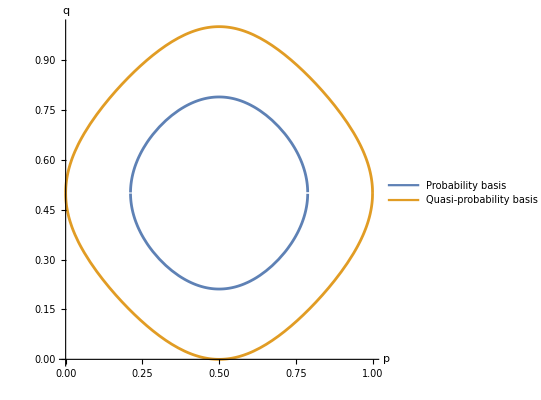

```mathematica
Plot[Evaluate[{q/. sol1,q/. sol2}],{p,0,1},PlotLegends->LineLegend[{ColorData[97][1],ColorData[97][2]},{"Probability basis","Quasi-probability basis"}],AxesLabel->{"p","q"},PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][2],ColorData[97][2]},AspectRatio->1]
```

#### Figure 7b

```mathematica
DensityPlot[
Evaluate[FullSimplify[σp σq]/. ℏ->1],{p,1/6 (3-Sqrt[3]),1/6 (3+Sqrt[3])},{q,1/6 (3-Sqrt[3] Sqrt[(-1+6 p-6 p^2)/(1-2 p+2 p^2)]),1/6 (3+Sqrt[3] Sqrt[(-1+6 p-6 p^2)/(1-2 p+2 p^2)])},FrameLabel->{"p","q"},ColorFunction->"SouthwestColors",PlotLegends->BarLegend[{"SouthwestColors",{1/(2 Sqrt[6]),1/2 (1-1/Sqrt[3])}},5,LegendLayout->"ReversedColumn"],PlotLabel->MaTeX[1/(2 Sqrt[6])<=Subscript[Δ,p] Subscript[Δ,q]<=1/2 (1-1/Sqrt[3])],PlotPoints->300]
```

-Graphics-

#### Figure 8

```mathematica
Plot3D[Evaluate[{1/2 Sqrt[3] (-1+2 p) (-1+2 q),FullSimplify[σp σq]/. ℏ->1}],{p,1/6 (3-Sqrt[3]),1/6 (3+Sqrt[3])},{q,1/6 (3-Sqrt[3] Sqrt[(-1+6 p-6 p^2)/(1-2 p+2 p^2)]),1/6 (3+Sqrt[3] Sqrt[(-1+6 p-6 p^2)/(1-2 p+2 p^2)])},Mesh->None,PlotPoints->100,PlotLegends->{MaTeX[TeXForm@"⟨Y⟩"],MaTeX[TeXForm@"ΔXΔZ"]},AxesLabel->{"p","q",MaTeX["\hbar",Magnification->2]}]
```

-Graphics3D-